## Analysis of SimTree output

```mathematica
demeCount=2;
```

## Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/bedfordt/Documents/current-projects/SimTree/source

```mathematica
SetOptions[Plot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLinePlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[ListLogPlot,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->{True,True,False,False},ImageSize->600,PlotRange->{0,All}];
```

```mathematica
SetOptions[Graphics,LabelStyle->Directive[Black,FontSize->9,FontFamily->"Helvetica"],Axes->False,Frame->False,FrameTicksStyle->Black,ImageSize->600,PlotRange->{0,All}];
```

```mathematica
colorlist={RGBColor[0.324,0.609,0.708],RGBColor[0.857,0.131,0.132]};
```

```mathematica
colorlist={RGBColor[0.765,0.728,0.274],RGBColor[0.324,0.609,0.708],RGBColor[0.857,0.131,0.132]};
```

```mathematica
colorrules=MapIndexed[#2[[1]]-1->#1&,colorlist]
```

{0→RGBColor[0.765,0.728,0.274],1→RGBColor[0.324,0.609,0.708],2→RGBColor[0.857,0.131,0.132]}

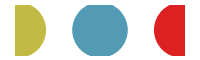

```mathematica
Graphics[{PointSize[0.2],MapIndexed[{#1,Point[{#2[[1]],0}]}&,colorlist]},AspectRatio->0.3,ImageSize->200]
```

## Assumptions

Let’s say there are 10 sites that function to move the virus in phenotype space

```mathematica
10*0.005*(1/365)
```

0.000136986

Mutations per day

## World-wide SIR

```mathematica
data=Import["out.timeseries","Table"];
```

```mathematica
TableForm[data[[1]],TableHeadings->{Range[30]}]
```

1 | date
2 | diversity
3 | totalN
4 | totalS
5 | totalI
6 | totalR
7 | totalCases
8 | northN
9 | northS
10 | northI
11 | northR
12 | northCases
13 | tropicsN
14 | tropicsS
15 | tropicsI
16 | tropicsR
17 | tropicsCases

```mathematica
data=Drop[data,1];
```

```mathematica
startTime=data[[1,1]]
```

0.0027

```mathematica
endTime=data[[-1,1]]
```

5.4795

```mathematica
popSize=data[[1,3]]
```

400000

### Prevalence

```mathematica
prev=data[[All,{1,5}]];
```

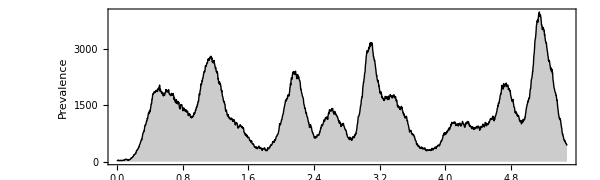

```mathematica
prevfig=ListLinePlot[prev,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->GrayLevel[0.8],FrameLabel->{"","Prevalence"},ImagePadding->{{40,10},{15,5}}]
```

### Incidence

```mathematica
inc=data[[All,{1,7}]];
```

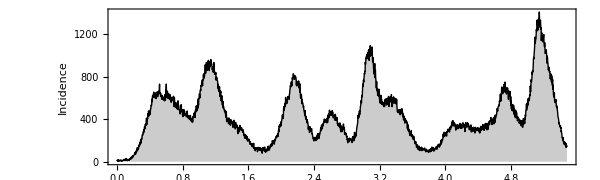

```mathematica
incfig=ListLinePlot[inc,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->GrayLevel[0.8],FrameLabel->{"","Incidence"},ImagePadding->{{40,10},{15,5}}]
```

Mean prevelance

```mathematica
N[Mean[prev[[All,2]]]]
```

1306.24

```mathematica
N[Mean[prev[[All,2]]]/popSize]
```

0.00326561

Mean incidence per year

```mathematica
N[(Total[inc[[All,2]]]/endTime)]
```

159271.

```mathematica
N[(Total[inc[[All,2]]]/endTime)/popSize]
```

0.398178

Flu incidence is 10% per year and prevalence is 0.14%.

### Diversity

```mathematica
div=data[[All,{1,2}]];
```

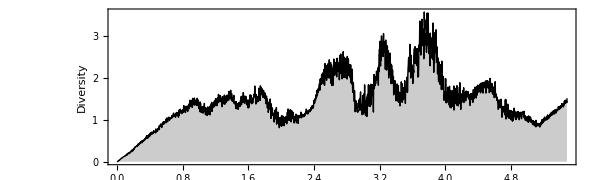

```mathematica
divfig=ListLinePlot[div,AspectRatio->0.3,Filling->Axis,PlotStyle->Black,FillingStyle->GrayLevel[0.8],FrameLabel->{"","Diversity"},ImagePadding->{{40,10},{15,5}}]
```

### Combined

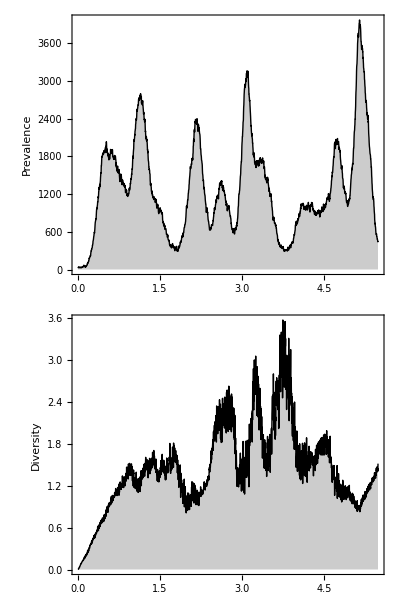

```mathematica
fig=Grid[{{prevfig},{divfig}}]
```

```mathematica
Export["timeseries.pdf",fig,"PDF"]
```

timeseries.pdf

## Regional SIR

```mathematica
data=Import["out.timeseries","Table"];
```

```mathematica
TableForm[data[[1]],TableHeadings->{Range[30]}]
```

1 | date
2 | diversity
3 | totalN
4 | totalS
5 | totalI
6 | totalR
7 | totalCases
8 | northN
9 | northS
10 | northI
11 | northR
12 | northCases
13 | tropicsN
14 | tropicsS
15 | tropicsI
16 | tropicsR
17 | tropicsCases

```mathematica
data=Drop[data,1];
```

```mathematica
startTime=data[[1,1]]
```

0.0027

```mathematica
endTime=data[[-1,1]]
```

5.4795

### Prevalence

```mathematica
Table[i,{i,10,10+(demeCount-1)*5,5}]
```

{10,15}

```mathematica
prevList=Table[data[[All,{1,i}]],{i,10,10+(demeCount-1)*5,5}];
```

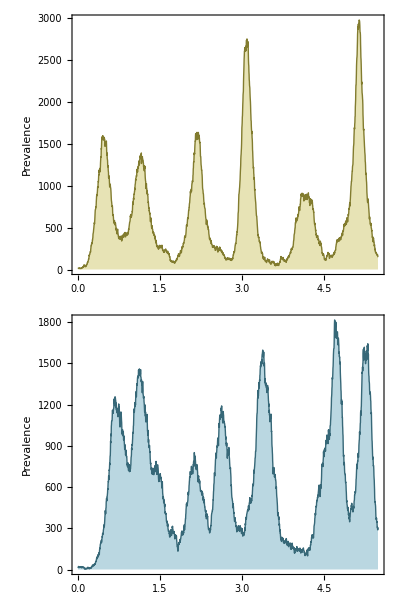

```mathematica
fig=Grid[Table[{ListLinePlot[prevList[[i]],AspectRatio->0.15,ImageSize->700,Filling->Axis,PlotStyle->Darker[colorlist[[i]]],FillingStyle->Directive[Opacity[0.4,colorlist[[i]]]],FrameLabel->{"","Prevalence"},ImagePadding->{{40,10},{15,5}}]},{i,demeCount}]]
```

```mathematica
Export["timeseriesSpatial.pdf",fig,"PDF"]
```

timeseriesSpatial.pdf

## Tip traits

```mathematica
data=Import["out.tips","CSV"];
```

```mathematica
Length[data]
```

40085

```mathematica
traitHeader=data[[1]];
```

```mathematica
TableForm[traitHeader,TableHeadings->{Range[4]}]
```

1 | name
2 | year
3 | location
4 | phenotype

```mathematica
data=Drop[data,1];
```

```mathematica
name=1;year=2;loc=3;ag1=4;ag2=5;
```

### Graphics settings

```mathematica
frameWindow=0.2;
```

```mathematica
plotRange={{Floor[Min[data[[All,ag1]]],frameWindow],Ceiling[Max[data[[All,ag1]]],frameWindow]},{Floor[Min[data[[All,ag2]]],frameWindow],Ceiling[Max[data[[All,ag2]]],frameWindow]}}
```

{{-0.4,3.},{0.,0.}}

```mathematica
aspectRatio=Max[Apply[EuclideanDistance,plotRange[[2]]]/Apply[EuclideanDistance,plotRange[[1]]],0.15]
```

0.15

```mathematica
imageSize=If[aspectRatio>1,600/aspectRatio,600]
```

600

```mathematica
frameTicks=Table[Table[{i,i,{0.01,0}},{i,-10,10,frameWindow}],{2},{2}];
```

### Year vs AG1

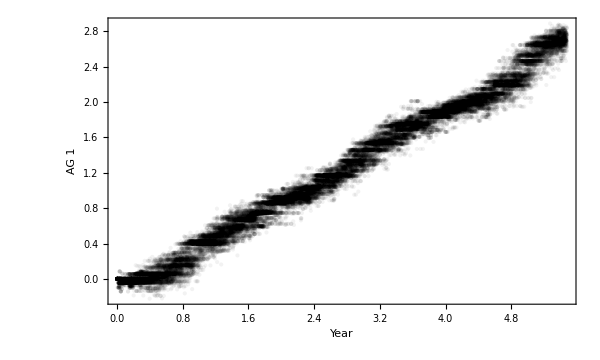

```mathematica
fig=ListPlot[data[[All,{year,ag1}]],AspectRatio->0.6,PlotRange->All,PlotStyle->Directive[PointSize[Medium],Black,Opacity[0.05]],FrameLabel->{"Year","AG 1"}]
```

```mathematica
Export["tipsYearAG1.pdf",fig,"PDF"]
```

tipsYearAG1.pdf

### Year vs AG2

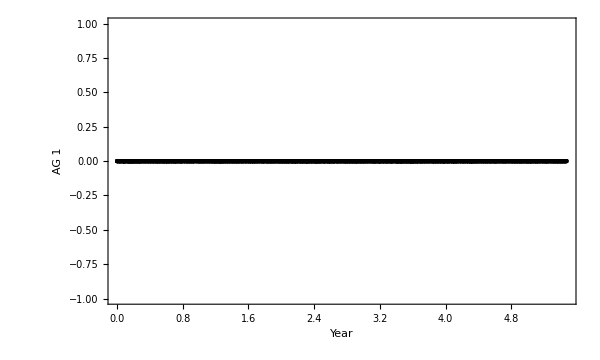

```mathematica
fig=ListPlot[data[[All,{year,ag2}]],AspectRatio->0.6,PlotRange->All,PlotStyle->Directive[PointSize[Medium],Black,Opacity[0.05]],FrameLabel->{"Year","AG 1"}]
```

```mathematica
Export["tipsYearAG2.pdf",fig,"PDF"]
```

tipsYearAG2.pdf

### AG1 vs AG2

```mathematica
tallies=Tally[data[[All,{ag1,ag2}]]];
```

```mathematica
points=Map[{PointSize[N[0.001*Sqrt[#[[2]]]]],Point[#[[1]]]}&,tallies];
```

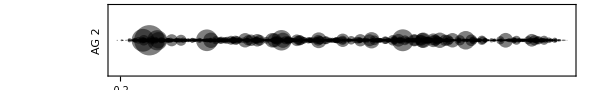

```mathematica
fig=Graphics[{Opacity[0.5],points},AspectRatio->aspectRatio,PlotRange->plotRange,ImageSize->imageSize,FrameLabel->{"AG 1","AG 2"},Frame->{True,True,False,False},FrameTicks->frameTicks]
```

```mathematica
Export["tipsAG1AG2.pdf",fig,"PDF"]
```

tipsAG1AG2.pdf

### Map

```mathematica
jitter=Flatten[Map[Table[#[[1]]+RandomVariate[NormalDistribution[0,0.017],2],{Round[0.02*#[[2]]]}]&,tallies],1];
```

```mathematica
Length[jitter]
```

544

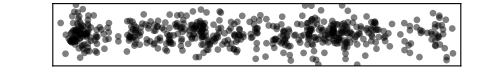

```mathematica
fig=ListPlot[jitter,AspectRatio->aspectRatio,PlotRange->plotRange,PlotStyle->Directive[PointSize[0.01],Black,Opacity[0.5]],GridLines->{Range[-10,10,frameWindow],Range[-10,10,frameWindow]},GridLinesStyle->GrayLevel[0.9],Frame->True,ImageSize->imageSize*0.8,FrameTicks->None]
```

```mathematica
Export["tipsMap.pdf",fig,"PDF"]
```

tipsMap.pdf

### Year vs AG1 - Spatial

```mathematica
points=Table[Select[data,#[[loc]]==i&][[All,{year,ag1}]],{i,0,demeCount-1}];
```

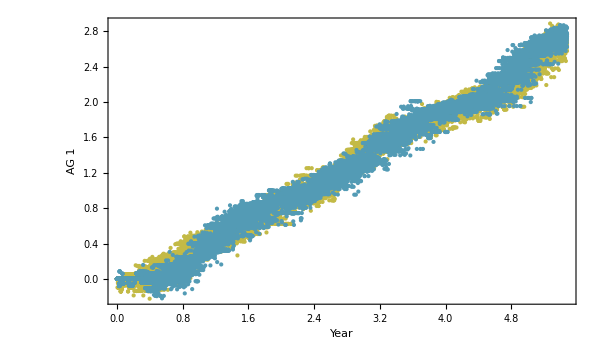

```mathematica
fig=ListPlot[points,AspectRatio->0.6,PlotRange->All,PlotStyle->colorlist,FrameLabel->{"Year","AG 1"}]
```

```mathematica
Export["tipsYearAG1Spatial.pdf",fig,"PDF"]
```

tipsYearAG1Spatial.pdf

## Trait history

```mathematica
TableForm[{"name","year","trunk","location","ag1","ag2"},TableHeadings->{Range[6]}]
```

1 | name
2 | year
3 | trunk
4 | location
5 | ag1
6 | ag2

```mathematica
name=1;year=2;trunk=3;loc=4;ag1=5;ag2=6;
```

```mathematica
data=ToExpression[Import["out.paths","Table"]];
```

$Aborted

```mathematica
interval=1;
```

```mathematica
Length[Range[1,Length[data],interval]]
```

405

```mathematica
sideBranches=Table[Select[data[[i]],#[[trunk]]==0&],{i,1,Length[data],interval}];
```

```mathematica
trunkBranches=Table[Select[data[[i]],#[[trunk]]==1&],{i,1,Length[data],interval}];
```

```mathematica
tips=DeleteCases[Map[If[Length[#]>0,#[[1]],Null]&,sideBranches],Null];
```

### 1D with trunk

```mathematica
branchScale=0.001;tipScale=0.005;clip=0.005;
```

```mathematica
xyBranches=Map[#[[All,{year,ag1}]]&,sideBranches];
```

```mathematica
xyPairs=Tally[Flatten[Map[Partition[DeleteDuplicates[#],2,1]&,xyBranches],1]];
```

```mathematica
xyBranchLines=Map[{Thickness[Clip[branchScale*N[Sqrt[#[[2]]]],{0,clip}]],Line[#[[1]]]}&,xyPairs];
```

```mathematica
xyBranches=Map[#[[All,{year,ag1}]]&,trunkBranches];
```

```mathematica
xyPairs=Tally[Flatten[Map[Partition[DeleteDuplicates[#],2,1]&,xyBranches],1]];
```

```mathematica
xyTrunkLines=Map[{Thickness[Clip[branchScale*N[Sqrt[#[[2]]]],{0,clip}]],Line[#[[1]]]}&,xyPairs];
```

```mathematica
xyPairs=Tally[tips[[All,{year,ag1}]]];
```

```mathematica
xyPoints=Map[{PointSize[N[tipScale*Sqrt[#[[2]]]]],Point[#[[1]]]}&,xyPairs];
```

```mathematica
branchLines={CapForm["Round"],Directive[GrayLevel[0.3],Opacity[1]],xyBranchLines};
```

```mathematica
trunkLines={CapForm["Round"],Directive[Red,Opacity[1]],xyTrunkLines};
```

```mathematica
tipPoints={Directive[Black,Opacity[0.5]],xyPoints};
```

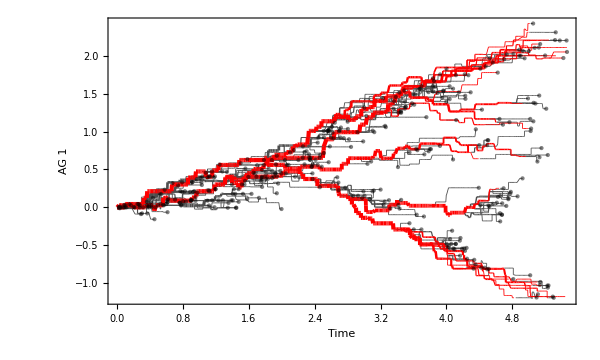

```mathematica
fig=Graphics[{branchLines,trunkLines,tipPoints},AspectRatio->0.6,PlotRange->All,ImageSize->600,FrameLabel->{"Time","AG 1"},Frame->{True,True,False,False}]
```

```mathematica
Export["pathsYearAG1.pdf",fig,"PDF"]
```

pathsYearAG1.pdf

### 2D with trunk

```mathematica
branchScale=0.001;tipScale=0.005;clip=0.005;
```

```mathematica
xyBranches=Map[#[[All,{ag1,ag2}]]&,sideBranches];
```

```mathematica
xyPairs=Tally[Flatten[Map[Partition[DeleteDuplicates[#],2,1]&,xyBranches],1]];
```

```mathematica
xyBranchLines=Map[{Thickness[Clip[branchScale*N[Sqrt[#[[2]]]],{0,clip}]],Line[#[[1]]]}&,xyPairs];
```

```mathematica
xyBranches=Map[#[[All,{ag1,ag2}]]&,trunkBranches];
```

```mathematica
xyPairs=Tally[Flatten[Map[Partition[DeleteDuplicates[#],2,1]&,xyBranches],1]];
```

```mathematica
xyTrunkLines=Map[{Thickness[Clip[branchScale*N[Sqrt[#[[2]]]],{0,clip}]],Line[#[[1]]]}&,xyPairs];
```

```mathematica
xyPairs=Tally[tips[[All,{ag1,ag2}]]];
```

```mathematica
xyPoints=Map[{PointSize[N[tipScale*Sqrt[#[[2]]]]],Point[#[[1]]]}&,xyPairs];
```

```mathematica
branchLines={CapForm["Round"],Directive[GrayLevel[0.3],Opacity[1]],xyBranchLines};
```

```mathematica
trunkLines={CapForm["Round"],Directive[Red,Opacity[1]],xyTrunkLines};
```

```mathematica
tipPoints={Directive[Black,Opacity[0.5]],xyPoints};
```

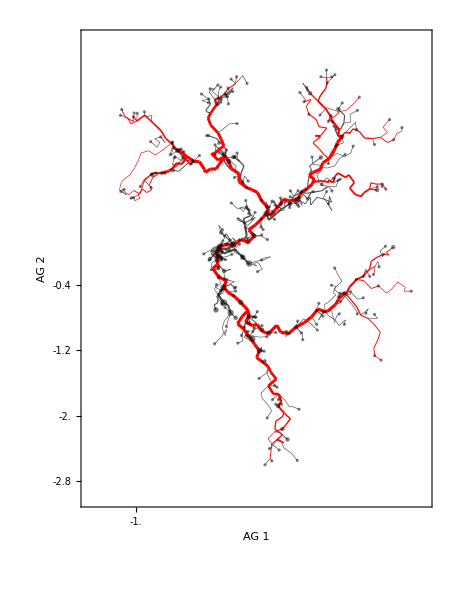

```mathematica
fig=Graphics[{branchLines,trunkLines,tipPoints},AspectRatio->aspectRatio,PlotRange->plotRange,ImageSize->imageSize,FrameLabel->{"AG 1","AG 2"},Frame->{True,True,False,False},FrameTicks->frameTicks]
```

```mathematica
Export["pathsAG1AG2.pdf",fig,"PDF"]
```

pathsAG1AG2.pdf

### 1D with location

```mathematica
branchScale=0.001;tipScale=0.005;clip=0.005;
```

```mathematica
xyzBranches=Map[#[[All,{year,loc,ag1}]]&,data];
```

```mathematica
xyzPairs=Tally[Flatten[Map[Partition[DeleteDuplicates[#],2,1]&,xyzBranches],1]];
```

```mathematica
xyBranchLines=Map[{Thickness[Clip[branchScale*N[Sqrt[#[[2]]]],{0,clip}]],#[[1,1,2]]/.colorrules,Line[#[[1,All,{1,3}]]]}&,xyzPairs];
```

```mathematica
branchLines={CapForm["Round"],xyBranchLines};
```

```mathematica
tipPoints=Map[{PointSize[tipScale],#[[2]]/.colorrules,Point[#[[{1,3}]]]}&,tips[[All,{year,loc,ag1}]]];
```

```mathematica
fig=Graphics[{branchLines,tipPoints},AspectRatio->0.6,PlotRange->All,ImageSize->600,FrameLabel->{"Time","AG 1"},Frame->{True,True,False,False}]
```

$Aborted[]

```mathematica
Export["pathsYearAG1Spatial.pdf",fig,"PDF"]
```

pathsYearAG1Spatial.pdf

## Genealogical tree

```mathematica
TableForm[{"name","year","trunk","location","ag1","ag2"},TableHeadings->{Range[6]}]
```

1 | name
2 | year
3 | trunk
4 | location
5 | ag1
6 | ag2

```mathematica
name=1;year=2;trunk=3;loc=4;ag1=5;ag2=6;
```

```mathematica
data=ToExpression[Import["out.paths","Table"]];
```

```mathematica
interval=10;
```

```mathematica
Length[Range[1,Length[data],interval]]
```

37

```mathematica
root=Last[Map[Last,data]][[1]]
```

55ad6c98

```mathematica
edgeLists=DeleteCases[Table[If[data[[i,-1,1]]==root,data[[i]],Null],{i,1,Length[data],interval}],Null];
```

```mathematica
edgeRules=Union[Flatten[Table[Map[#[[1,name]]->#[[2,1]]&,Partition[edgeLists[[i]],2,name]],{i,1,Length[edgeLists]}]]];
```

```mathematica
Length[edgeRules]
```

2159

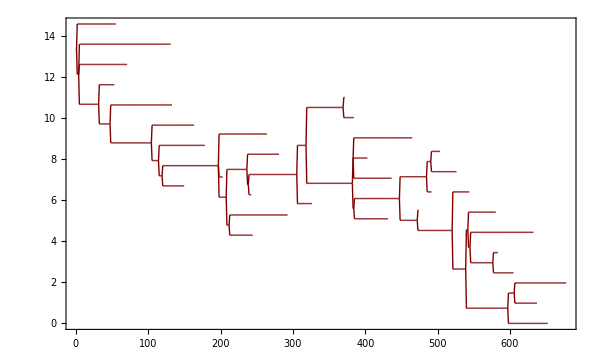

```mathematica
TreePlot[edgeRules,Left,root,VertexRenderingFunction->None,AspectRatio->0.6,Frame->{True,True,False,False},FrameTicks->Automatic]
```

```mathematica
vertices=Flatten[Map[First,edgeLists,{2}]];
```

```mathematica
coordinates=Join[{root->{0,0}},Map[#->Automatic&,DeleteCases[vertices,root]]];
```

```mathematica
Length[vertices]
```

12804

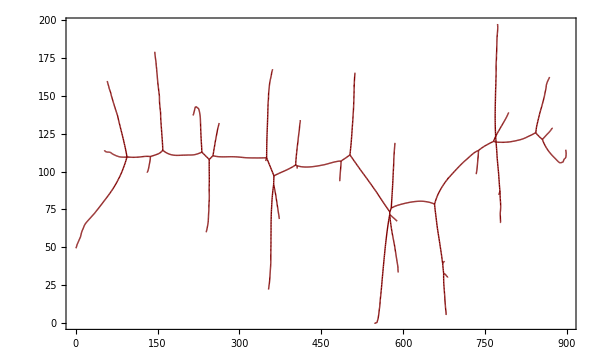

```mathematica
GraphPlot[edgeRules,VertexRenderingFunction->None,AspectRatio->0.6,Method->"SpringElectricalEmbedding",Frame->{True,True,False,False},FrameTicks->Automatic]
```

```mathematica
root=Last[Map[Last,data]][[1]]
```

55ad6c98

```mathematica
edgeLists=DeleteCases[Table[If[data[[i,-1,1]]==root,data[[i]],Null],{i,1,Length[data],interval}],Null];
```

```mathematica
edges=Union[Flatten[Table[Map[UndirectedEdge[#[[1,name]],#[[2,name]]]&,Partition[edgeLists[[i]],2,name]],{i,1,Length[edgeLists]}]]];
```

```mathematica
vertices=Flatten[Map[First,edgeLists,{2}]];
```

```mathematica
vertices=Join[{root},DeleteCases[vertices,root]];
```

```mathematica
Length[vertices]
```

12770

```mathematica
coordinates=Join[{{0,0}},Table[Automatic,{Length[vertices]-1}]];
```

```mathematica
TreeGraph[vertices,edges,AspectRatio->0.6,EdgeShapeFunction->"Line",VertexSize->0.0000001]
```

-Graphics-

```mathematica
Graph[edges,AspectRatio->0.6,EdgeShapeFunction->"Line",VertexSize->0.0000001,GraphLayout->"SpringElectricalEmbedding"]
```

-Graphics-